# Simulation of the max stationary values inDirected Configuration Model (DCM) with power-law in-degree distribution

## Setup

Load the package for simulation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<DCM`
```

Out-degree.

```mathematica
r0=2;
```

Where to cut-off max degree.

```mathematica
p0=1/2;
```

```mathematica
totalVariation[m0_,m1_]:=Norm[m0-m1,1]/2;
```

```mathematica
hh[degseq_]:=N[(degseq⟦1⟧ .Log[degseq⟦2⟧])/Total[degseq[[1]]]];
```

## Degree sequences

## Parallel Setup

```mathematica
LaunchKernels[2]
```

{KernelObject[…],KernelObject[…]}

```mathematica
SetSharedFunction[pdf0,pdf1]
```

```mathematica
ParallelNeeds["DCM`"]
```

## PDF — infinite variance case

We will first simulate DCM with out-degree fixed to be r0 and in-degree with heavy tail distribution with index

```mathematica
κ0=3/2;
```

The distribution.

```mathematica
dist0=heavyTailDist[κ0,r0]
```

ProbabilityDistribution[Piecewise[{{2/(x^(5/2) (-1+Zeta[3/2])), x≥2}, {(1+Zeta[3/2]-2 Zeta[5/2])/(-1+Zeta[3/2]), x==0}, {0, True}}],{x,0,∞,1}]

The PDF of this distribution

```mathematica
pdf0[i_]=PDF[dist0,i]
```

Piecewise[{{2/(i^(5/2) (-1+Zeta[3/2])), i≥2}, {(1+Zeta[3/2]-2 Zeta[5/2])/(-1+Zeta[3/2]), i==0}, {0, True}}]

Moments

```mathematica
Moment[dist0,1]
```

2

The 2nd moment is actually infinite

```mathematica
SumConvergence[i^2*pdf0[i],i]
```

False

## PDF1 — infinite variance case

We will then simulate DCM with out-degree fixed to be r0 and in-degree with heavy tail distribution with index

```mathematica
κ1=5/2;
```

The distribution.

```mathematica
dist1=heavyTailDist[κ1,r0]
```

ProbabilityDistribution[Piecewise[{{2/(x^(7/2) (-1+Zeta[5/2])), x≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), x==0}, {0, True}}],{x,0,∞,1}]

The PDF of this distribution

```mathematica
pdf1[i_]=PDF[dist1,i]
```

Piecewise[{{2/(i^(7/2) (-1+Zeta[5/2])), i≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), i==0}, {0, True}}]

Moments

```mathematica
Moment[dist1,1]
```

2

The 2nd moment is finite

```mathematica
Moment[dist1,2]//N//Quiet
```

9.44325

## Simulation

Size of the graph

```mathematica
n1=10000
```

10000

```mathematica
simMixing[pdf_,n1_,r0_,p0_]:=Module[{m1,degseq,heads,tails,hh1,tent1,g1,trans1,transM,pi1,distList,i,dist,maxdeg},m1=n1 r0;degseq=pdf2Deg[pdf,r0,n1,p0];
maxdeg=degseq[[1,-1]];{heads,tails}=deg2Stub/@degseq;hh1=hh[degseq];tent1=Log[n1]/hh1;g1=makeDCM[n1,heads,tails];trans1=transitProbM[g1];pi1=stationaryProbEigen[g1];distList={};
transM=trans1;
For[i=0,i≤3/2 tent1,i++,
dist=Max[(totalVariation[#1,pi1]&)/@transM];
AppendTo[distList,dist];
PrintTemporary[i];
transM=transM.trans1
];{tent1,maxdeg,distList}]
```

```mathematica
?pdf0
```

```mathematica
?pdf1
```

```mathematica
AbsoluteTiming[data=ParallelTable[simMixing[pdf,n1,r0,p0],{pdf,{pdf0,pdf1}}]]
```

0

0

1

1

2

2

3

3

4

4

5

5

6

6

7

7

8

8

9

9

10

10

11

11

12

12

13

13

14

14

15

16

15

17

16

18

17

19

18

19

{2377.23,{{13.2877,58,{1.,1.,0.999818,0.997569,0.993201,0.979039,0.958545,0.905872,0.835783,0.707892,0.577502,0.449402,0.336061,0.245748,0.175084,0.124587,0.088788,0.0630393,0.0444843,0.0312389}},{13.2877,29,{1.,0.999991,0.999618,0.998796,0.996269,0.989435,0.97608,0.948375,0.903386,0.824869,0.701961,0.549332,0.408575,0.295593,0.210422,0.150742,0.106233,0.0747994,0.0531329,0.038104}}}}

```mathematica
{tent0,maxdeg0,distList0}=data[[1]]
```

{13.2877,58,{1.,1.,0.999818,0.997569,0.993201,0.979039,0.958545,0.905872,0.835783,0.707892,0.577502,0.449402,0.336061,0.245748,0.175084,0.124587,0.088788,0.0630393,0.0444843,0.0312389}}

```mathematica
{tent1,maxdeg1,distList1}=data[[2]]
```

{13.2877,29,{1.,0.999991,0.999618,0.998796,0.996269,0.989435,0.97608,0.948375,0.903386,0.824869,0.701961,0.549332,0.408575,0.295593,0.210422,0.150742,0.106233,0.0747994,0.0531329,0.038104}}

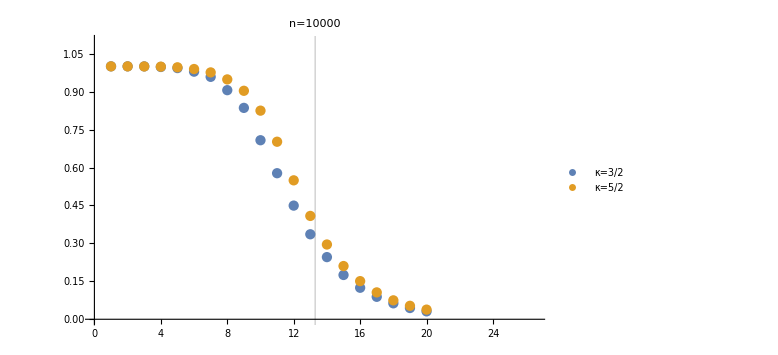

```mathematica
plt=ListPlot[{distList0,distList1},GridLines->{{tent0,tent1}, {}},BaseStyle->{FontSize->25},ImageSize->Large,PlotLegends->LineLegend[(StringForm["κ=``",#]&/@{κ0,κ1}),LabelStyle->{FontSize->25}],PlotLabel->StringForm["n=``",n1],PlotRange->{{0,2tent0},{0,1.1}}]
```

```mathematica
Export["mixing-1.pdf",plt]
```

mixing-1.pdf